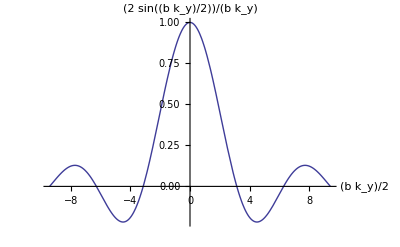

```mathematica
Plot[ Sin[x]/(x), 
{x, -3 Pi, 3 Pi},
Ticks -> {{ -2 Pi, -Pi, 0,  Pi,  2 Pi}},
AxesLabel -> { b Subscript[k, y]/2, Sin[ b Subscript[k, y]/2]/(b Subscript[k, y]/2)}
]
```

```mathematica
Manipulate[
Module[
{beta, gamma, k},
k = 2 Pi (*/ (650 10^(-9))*) ;
beta = b k Sin[theta] /2 ;
gamma = a k Sin[theta]/2 ;
Plot[ (Sin[beta]/beta)^2 (Sin [n gamma]/ Sin[gamma])^2, {theta, -Pi, Pi}
, PlotRange -> Full]
],
{{b, 0.172}, 0.01, 1},
{{a, 0.869}, 0.01, 1},
{{n, 5}, 1, 30, 1}
]
```